# ^135Pr - energy Ellipsoid

## A classical approach for obtaining the energy of the rigid rotor

## Numerical application -> obtained by fitting the experimental values of the excitation energies

By using the parameters obtained from the fit of the excitation energies (through a least squares procedure), the numerical values of the necessary terms which enter in the parametrization of the classical energy function H’ can be calculated. The classical energy function is expressed in the following parameters:
	u=(A_3-A_1)/A=f(𝕏)
𝕏={I,j,A_1,A_2,A_3,θ_coupling}
v_0=-(A_1 j_1)/A=g(𝕏)

𝔛 - the fixed set of parameters which will be initialized with the corresponding values from the r.m.s. fit.

## Approach

By doing a diagonalization of the Hamiltonian H’ written in terms of the classical components of the angular momentum I, and the Poisson bracket as the corresponding algebra, one can obtain a classical expression for the energy function, in terms of coordinates which are related to the actual angular momentum  components (I_1,I_2,I_3).

The particular case of Maximal Moment of Inertia along the first axes. ℐ_1- maximal moi

Expressing H’ in terms of the spherical coordinates (φ_1,θ_1) we get the following formula: 

					H'=(cos^2 φ+u sin^2 φ)(I^2-x_1^2)+2 v_0 x_1
which then we can further expand into the spherical coordinates:
					H' (θ_1,φ_1)=(cos^2 φ+u sin^2 φ)(1-cos^2 θ_1)I^2+2I v_0 cosθ

## Numerical calculations

### The obtained fit parameters

```mathematica
I1=89;
I2=12;
I3=48;
THETA=N[-71*π/180];
(*I1=20;
I2=100;
I3=40;
THETA=N[π/6];*)
```

### Fixed constants

```mathematica
SPIN=19/2;
j=N[11/2];
quantSpin=SPIN+2;
(*SPIN=45/2;
j=N[13/2];*)
```

### Inertia factors

```mathematica
A1=1/(2*I1);
A2=1/(2*I2);
A3=1/(2*I3);
```

## Inertial functions

The inertial terms which enter in the expression of the Hamiltonian H’

```mathematica
Afct[spin_,oddspin_,a1_,a2_,th_]:=a2(1-(oddspin*Sin[th])/spin)-a1;
ufct[spin_,oddspin_,a1_,a2_,a3_,th_]:=(a3-a1)/Afct[spin,oddspin,a1,a2,th];
v0fct[spin_,oddspin_,a1_,a2_,th_]:=-(a1*oddspin*Cos[th])/Afct[spin,oddspin,a1,a2,th];
vfct[spin_,oddspin_,a1_,a2_,th_]:=v0fct[spin,oddspin,a1,a2,th]/spin;
```

### Numerical values for the inertial parameters (u,v_0) based on the fixed parameter set - 𝔛

```mathematica
u[spin_]:=N[ufct[spin,j,A1,A2,A3,THETA]];
v0[spin_]:=N[v0fct[spin,j,A1,A2,THETA]];
k[spin_]:=N[√ufct[spin,j,A1,A2,A3,THETA]];
```

```mathematica
u[19/2]
```

0.081531

```mathematica
v0[19/2]
```

-0.170917

```mathematica
v0[19/2]/(19/2)
```

-0.0179912

### The components of angular momentum

```mathematica
x1[spin_,theta_]:=spin*Cos[theta];
```

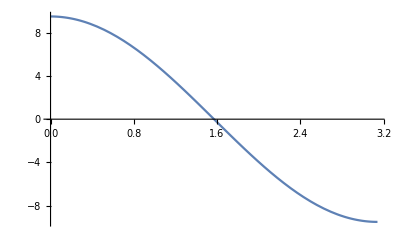

```mathematica
Plot[x1[SPIN,x],{x,0,π}]
```

## Energy function H’

## Expressed in terms of spherical coordinates (θ_1,φ_1)

```mathematica
EnSph[spin_,theta_,fi_]:=(Cos[fi]^2+u[spin] Sin[fi]^2)(1-Cos[theta]^2)spin^2+2v0[spin]*spin*Cos[theta];
```

## Expressed in terms of angular coordinates (x_1,φ_1)

```mathematica
EnAng[spin_,x11_,fi_]:=(Cos[fi]^2+u[spin] Sin[fi]^2)(spin^2-x11^2)+2v0[spin]*x11;
```

## First stationary point

```mathematica
P0[spin_]:={ArcCos[v0[spin]/(u[spin]*spin)],π/2};
```

## Second stationary point

```mathematica
P1[spin_]:={ArcCos[v0[spin]/spin],0};
```

## The energy function in the minimum points

```mathematica
En0min[spin_]:=EnSph[spin,P0[spin][[1]],P0[spin][[2]]];
En1min[spin_]:=EnSph[spin,P1[spin][[1]],P1[spin][[2]]];
```

```mathematica
En0min[SPIN]
```

7.71647

```mathematica
En1min[SPIN]
```

90.2792

## Test the numerical value with the analytical formula E_s=(u+v^2/u)I^2 and E_M=I^2+v^2

```mathematica
N[(u[SPIN]+v0[SPIN]^2/(SPIN^2 u[SPIN]))SPIN^2]
```

7.71647

```mathematica
N[(SPIN^2+v0[SPIN]^2)]
```

90.2792

```mathematica
saddlePoint=Graphics[Style[Point[P0[SPIN]],Red,PointSize[0.02]]];
maxPoint=Graphics[Style[Point[P1[SPIN]],Blue,PointSize[0.02]]];
```

## color function

```mathematica
CoolColor[ z_ ] :=RGBColor[z,1-z,1];
```

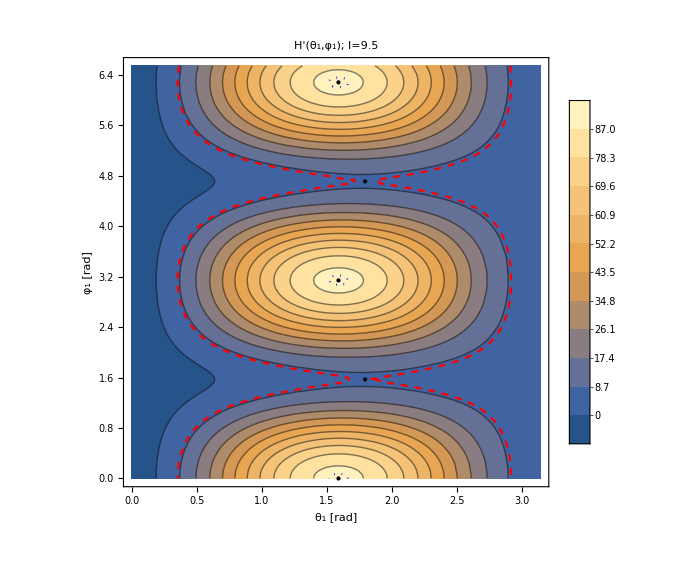

```mathematica
energyfunction[spin_]:=ContourPlot[EnSph[spin,theta,fi],{theta,0,π},{fi,0,2π+π/12},PlotLabel->StringTemplate["H'(θ_1,φ_1); I=``"][SPIN],FrameLabel->{"θ_1 [rad]","φ_1 [rad]"},Contours->11,PlotLegends->Automatic,PlotRange->{-5,100},LabelStyle->{17,Bold,Black,FontFamily->"Times New Roman"}];
Show[{energyfunction[SPIN],ContourPlot[EnSph[SPIN,theta,fi]==En0min[SPIN],{theta,0,π},{fi,0,2π+π/12},ContourStyle->{Thick,Dashed,Red}],ContourPlot[EnSph[SPIN,theta
,fi]==En1min[SPIN]-0.5,{theta,0,π},{fi,0,2π+π/12},ContourStyle->{Dotted,Blue}],saddlePoint,maxPoint,Graphics[Style[Point[{P0[SPIN][[1]],P0[SPIN][[2]]+π}],Red,PointSize[0.02]]],Graphics[Style[Point[{P1[SPIN][[1]],P1[SPIN][[2]]+π}],Blue,PointSize[0.02]]],Graphics[Style[Point[{P1[SPIN][[1]],P1[SPIN][[2]]+2π}],Blue,PointSize[0.02]]]},ImageSize->Large]
```

```mathematica
|
```

## Dynamic representation for the contour plot

```mathematica
Manipulate[Show[{ContourPlot[EnSph[spini,theta,fi],{theta,0,π},{fi,0,2π},PlotLabel->StringTemplate["H'(θ_1,φ_1); I=``"][spini],FrameLabel->{"θ_1 [rad]","φ_1 [rad]"},Contours->11,PlotLegends->Automatic,PlotRange->Automatic,LabelStyle->{17,Bold,Black,FontFamily->"Times New Roman"}],ContourPlot[EnSph[spini,theta,fi]==En0min[spini],{theta,0,π},{fi,0,2π},ContourStyle->{Thick,Dashed,Red}],ContourPlot[EnSph[spini,theta
,fi]==En1min[spini]-0.5,{theta,0,π},{fi,0,2π},ContourStyle->{Dotted,Blue}],saddlePoint,maxPoint},ImageSize->Large],{spini,5.5,30.5,2}]
```

Show::gcomb: Could not combine the graphics objects in ….

## 3D Plot for the energy function H’ as function of (θ_1,φ_1)

```mathematica
Show[Plot3D[EnSph[SPIN,theta,fi],{theta,0,π},{fi,0,2π},AxesLabel->{"θ_1","φ_1"},ImageSize->Large,ColorFunction->"DarkRainbow",PlotLabel->Style["Energy function - 3D representation",18,Bold,Black,Italic,FontFamily->"Times new Roman"],AxesStyle->Directive[{Thick,Black,18,Bold,FontFamily->"Times New Roman"}],PlotLegends->Automatic],Graphics3D[Style[Point[{P0[SPIN][[1]],P0[SPIN][[2]],En0min[SPIN]}],Red,PointSize[0.02]]],Graphics3D[Style[Point[{P0[SPIN][[1]],P0[SPIN][[2]]+π,En0min[SPIN]}],Red,PointSize[0.02]]],Graphics3D[Style[Point[{P1[SPIN][[1]],P1[SPIN][[2]],En1min[SPIN]}],Blue,PointSize[0.02]]],Graphics3D[Style[Point[{P1[SPIN][[1]],P1[SPIN][[2]]+π,En1min[SPIN]}],Blue,PointSize[0.02]]],Graphics3D[Style[Point[{P1[SPIN][[1]],P1[SPIN][[2]]+2π,En1min[SPIN]}],Blue,PointSize[0.02]]],Epilog->Inset[Framed[Style[TemplateApply[StringTemplate["I= ``"][SPIN]],20,Italic,Bold,Black,FontFamily->"Times New Roman"],Background->None],{Right,Bottom},{Right,Bottom}]]
```

-Graphics3D-

## The potential energy V(q) of the rotor for the fixed parameters

```mathematica
Vrotor[q_,spin_]:=(spin*(spin+1)*k[spin]^2+v0[spin]^2)*JacobiSN[q,k[spin]^2]^2+(2*spin+1)*v0[spin]*JacobiCN[q,k[spin]^2]*JacobiDN[q,k[spin]^2];
```

```mathematica
Manipulate[Plot[Vrotor[x,spino],{x,-8,8},Frame->True,AspectRatio->0.5,PlotStyle->{Red,Thick},FrameLabel->{"q","V(q)"},Epilog->Inset[Graphics[Text[Style[StringTemplate["I=``\n ℐ_1:ℐ_2:ℐ_3 = ``:``:``"][spino,I1,I2,I3],17,Bold,Black,FontFamily->"Times New Roman"]]],Scaled[{0.3,0.2}]],ImageSize->Large,FrameStyle->Directive[Black,Thick],Axes->False,LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"}],{spino,5.5,30.5,2}]
```

## Revolution plot for the Potential V(q)

```mathematica
RevolutionPlot3D[Vrotor[x,SPIN],{x,-8,8},ColorFunction->"DarkRainbow"]
```

-Graphics3D-

## Spherical plot for the energy function H’

## Quantization of the first axis - maximal MOI is ℐ_1

```mathematica
p1=Graphics3D[{Black,Thick,Arrow[{{0,0,0},{0,0,SPIN+quantSpin}}],Black,Thick,Arrow[{{0,0,0},{0,SPIN+quantSpin,0}}],Red,Thick,Arrow[{{0,0,0},{SPIN+quantSpin,0,0}}]}];
```

## spherical coordinates (quantization on 1-axis)

```mathematica
x1[r_,theta_,fi_]:=r Cos[theta];x2[r_,theta_,fi_]:=r Sin[theta]Cos[fi];x3[r_,theta_,fi_]:=r Sin[theta]Sin[fi];
```